```mathematica
Melanoma Skin Cancer Detection using ANN
```

```mathematica
Design of a computer-based system to automatically classify histopathological images of skin tissue
```

```mathematica
Importing Data - Training & Testing Set
```

```mathematica
nImages = 100; (* number of sample images *)
nTrainset = 70; (* number of images used for training the ANN *)
data = Import["ImageData.xlsx", {"Data",1,Range[2,nImages+1],{1,2,3}}]; (* data file has a header in row 1 *)
target =  Import["ImageData.xlsx", {"Data",1,Range[2,nImages+1],4}];  (* 4th column corresponds to the ground truth *)
trainindex = RandomSample[Range[2,nImages],nTrainset]; (* Randomly split images betweeen training and testing set *)
testindex= Complement[Range[2,nImages], trainindex];
```

```mathematica
Defining the ANN with 1 hidden layer
```

```mathematica
inNum = 3; hidNum = 3; outNum =1; (* 3 input units, 3 hidden units and 1 output unit *)
wh = Table[Table[Random[Real, {-2.5,2.5}],{inNum}],{hidNum}]; (* hidden weights *)
wo = Table[Table[Random[Real, {-2.5,2.5}],{hidNum}],{outNum}]; (* output weights *) 
eta = 0.5;(* learning rate *)
```

```mathematica
sigmoid[x_]:= 1/(1+Exp[-x]); relu[x_]:=Map[Max[0,#]&,x]; (* activation functions *) 
l = nTrainset; (* number images in the training set *)
```

```mathematica
(* funtion to train the ANN *) 
TrainEpochs[n_]:= Module[{iter = nTrainset},Table[
If[k≤ l,r=trainindex[[k]],r = trainindex[[Mod[k,l]+1]]];
in=data[[r]];
y=target⟦r⟧;
outhid = sigmoid[wh.in];
out = sigmoid[wo.outhid];
e = y-out;
outdelta = e out(1-out);
hiddelta = outhid(1-outhid) Transpose[wo].outdelta;
wo+= eta e.e Outer[Times, outdelta,outhid];
wh+= eta e.e Outer[Times, hiddelta, in]; 
{e.e, wo, wh},{k,1,iter}]];
```

```mathematica
(* function to evaluate the ANN *) 
EvalNetwork[in_]:=Module[{outhid},outhid = sigmoid[wh.in];
sigmoid[wo.outhid]]
```

```mathematica
(* function to compute the testing error *) 
testErrorfunc[n_]:= Module[{},RootMeanSquare[Table[target[[testindex[[i]]]]- EvalNetwork[data[[testindex[[i]]]]],{i,1,nImages-nTrainset-1}]//Flatten]//N]
```

Training the ANN

```mathematica
nIterations = 15; (* number of iterations *)
ErrorList=Table[{TrainEpochs[1],testErrorfunc[k]},{k,1,nIterations}];
```

```mathematica
colors={Green,Red,Orange,Blue,Gray};
```

```mathematica
trainplot=Table[ListPlot[ ErrorList[[pp,1,All,1]]//Flatten, PlotJoined -> True, Frame->True, FrameLabel->{"Image Number","SquaredError"},PlotRange->All,PlotStyle->colors[[Mod[pp,5]]]],{pp,1,nIterations}];
```

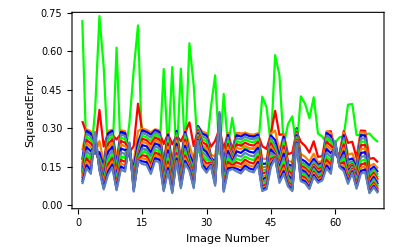

```mathematica
Show[trainplot]
```

```mathematica
Performance Evaluation
```

```mathematica
TP=0; FP=0; TN=0;FN=0; (* true positives, false positives, true negatives and false negatives *)
For[i=1, i≤ Length[testindex], i++, 
in = data[[testindex[[i]]]];
y = target[[testindex[[i]]]];
outhid = sigmoid[wh.in];
out = Round[sigmoid[wo.outhid]];
Which[out[[1]]== y==1, TP+= 1, out[[1]]== y==0, TN+= 1, 
out[[1]] ≠ y&&out [[1]]== 0, FN+= 1,out[[1]]≠ y && out[[1]] == 1, FP+= 1]
];
```

```mathematica
(* Compute True Positive Rate (TPR), also called recall or sensitivity*) 
NSensitivity = TP / (TP + FN);
(* Compute Precision, also called Positive Predictive Value (PPV)*) 
NPrecision = TP / (TP + FP);
(*Compute True Negative Rate (TNR), also called specificity*)
NSpecificity = TN / (TN+ FP);
(* Compute Accuracy*) 
NAccuracy = (TP + TN) / (TP + TN + FP + FN);
```

```mathematica
Print["Sensitivity","=",N[NSensitivity,3]]
Print["Precision","=",N[NPrecision,3]]
Print["Specificity","=",N[NSpecificity,3]]
Print["Accuracy","=",N[NAccuracy,3]]
```

Sensitivity=1.

Precision=0.875

Specificity=0.867

Accuracy=0.931

```mathematica
Visualizing the Classification Task
```

```mathematica
signal=Position[target,_?(#==1.&)]//Flatten;
bckg=Position[target,_?(#==0.&)]//Flatten;
signaldata=Map[data[[#]]&,signal];
bckgdata=Map[data[[#]]&,bckg];
ip=ListPointPlot3D[{signaldata,bckgdata}];
op=ContourPlot3D[EvalNetwork[{xx,yy,zz}]==1/2,{xx,-4,4},{yy,-4,4},{zz,-4,4}];
Show[op,ip]
```

-Graphics3D-

```mathematica
Assessing Overfitting - Training&Testing Error
```

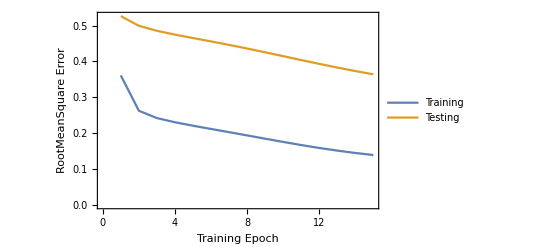

```mathematica
trainingError=Table[RootMeanSquare[ErrorList[[i,1,All,1]]],{i,1,nIterations}];
testError=Table[ErrorList[[i,2]],{i,1,nIterations}];
ListLinePlot[{trainingError,testError},Frame->True,FrameLabel->{"Training Epoch", "RootMeanSquare Error"},PlotLegends-> {"Training", "Testing"}]
```